## 情報数学レポート 1SC16309Y田中雅也

## 課題

#### 問題 1. ∫_0^π Sin[x]ⅆx の値を近似計算する.

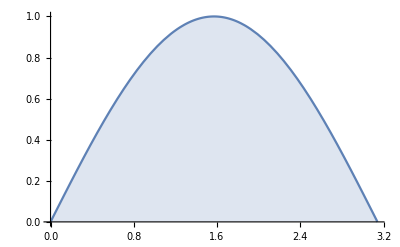

```mathematica
Plot[Sin[x],{x,0,π},Filling->Axis]
```

∑_(i=0)^(n-1) Sin[(π i)/n](π/n) が積分の近似値である.

(1)  n = 100 と n = 1000 のときに上記の和の値を数値(近似値)で求めよ.

```mathematica
n=100のとき
```

```mathematica
N[Sum[Sin[(π i)/100](π/100),{i,0,99}]]
```

1.99984

```mathematica
n=1000のとき
```

```mathematica
N[Sum[Sin[(π i)/1000](π/1000),{i,0,999}]]
```

2.

(2) ∫_0^π Sin[x]ⅆx の値をMathematicaのIntegral関数を用いて計算せよ.

```mathematica
Clear[x];N[∫_0^π Sin[x]ⅆx]
```

2.

#### 問題 2.∫_-1^1 2 √(1-x^2)ⅆx の値を近似計算する.

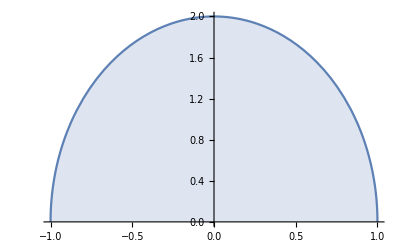

```mathematica
Plot[2 √(1-x^2),{x,-1,1},Filling->Axis]
```

(1) 問題 1. と同様に積分の近似値をΣを用いて表せ.

∑_(i=0)^(n-1) 2 √(1-((2i)/n-1)^2)(2/n)    すなはち　∑_(i=0)^(n-1) 4/n √((4i)/n(1-i/n))が積分の近似値である。

```mathematica
∑_(i=0)^(n-1) 2/n(2 √(1-((2i)/n-1)^2))
```

(2)  n = 100 と n = 1000 のときに上記の和の値を数値(近似値)で求めよ.

n = 100 のとき

```mathematica
N[Sum[4/100 √((4×i)/100(1-i/100)),{i,0,99}]]
```

3.13827

n = 1000 のとき

```mathematica
N[Sum[4/1000 √((4×i)/1000(1-i/1000)),{i,0,999}]]
```

3.14149

答え合わせ

```mathematica
Clear[x];N[∫_-1^1 2 √(1-x^2)ⅆx]
```

3.14159

```mathematica
n=100のとき
```

```mathematica
N[Sum[2/100(2 √(1-((2i)/100-1)^2)),{i,0,99}]]
```

3.13827

```mathematica
n=1000のとき
```

```mathematica
N[Sum[2/1000(2 √(1-((2i)/1000-1)^2)),{i,0,999}]]
```

3.14149

(3)∫_-1^1 2 √(1-x^2)ⅆx の値をMathematicaのIntegral関数を用いて計算せよ.

```mathematica
Integrate[2 √(1-x^2),{x,-1,1}]
```

π

```mathematica
Clear[x];N[∫_-1^1 2 √(1-x^2)ⅆx]
```

3.14159

(4) 積分値と(1)の近似値を10桁以上の精度で計算したとき, 正しい積分値と小数点以下6桁目を四捨五入して小数点以下5桁まで等しくなるためには n はいくつ以上である必要があるか?

n = 5737 のとき

```mathematica
N[Sum[4/5737 √((4×i)/5737(1-i/5737)),{i,0,5736}]]
```

3.14158

n = 5738 のとき

```mathematica
N[Sum[4/5738 √((4×i)/5738(1-i/5738)),{i,0,5737}]]
```

3.14159

よって、nは5738以上

```mathematica
n=5737のとき
```

```mathematica
N[Sum[2/5737(2 √(1-((2i)/5737-1)^2)),{i,0,5736}]]
```

3.14158

```mathematica
n=5738のとき
```

```mathematica
N[Sum[2/5738(2 √(1-((2i)/5738-1)^2)),{i,0,5737}]]
```

3.14159

```mathematica
よってn=5738である。
```

#### 問題 3.

関数 f[x] と区間 [a,b] と分割数 n が与えられたとき,
∑_(i=0)^(n-1) f[a+((b-a)i)/n](b-a)/n は積分 ∫_a^b f[x]ⅆx の近似値を与える.

(1) ∑_(i=0)^(n-1) f[a+((b-a)i)/n](b-a)/n を計算する関数 MyIntegral[f,a,b,n] を作成せよ.

```mathematica
Clear[f,a,b,n];MyIntegral[f_,a_,b_,n_]:=N[Sum[f[a+((b-a)i)/n](b-a)/n,{i,0,n-1}]]
```

(2) MyIntegral[Function[x, -x (x - 3)], 0, 3, 1000] を計算せよ.

```mathematica
MyIntegral[Function[x,-x(x-3)],0,3,1000]
```

4.5